Question Question (14 marks)

In the “Great Fun” amusement park there is a small train called Puffing Berty which does a circuit of the park.  The continuous random variable T, the time in minutes for a circuit to be completed, has a probability density function f with rule

f(t)=Piecewise[{{1/100(t-10)
1/100(30-t), 10≤t≤20

20≤t≤30}, {0, elsewhere}}]

a.	Sketch the graph of y=f(x).

2 marks

f[t_]:=Piecewise[{{1/100(t-10),10≤t≤20},{1/100(30-t),20≤t≤30},{0,x<10||x>30}}]

Plot[f[t],{t,-10,50},AxesLabel→{"time (mins)","Pr(T=t)"}]

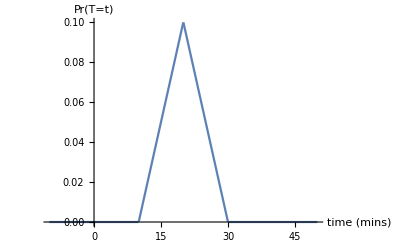

The graph must include the 0, elsewhere section, or it is not a probability density function.

b.	Find the probability that the time taken by Puffing Berty to complete a full circuit is less than 25 minutes.  (Give the exact value).

2 marks

(*Pr(T<25)*)
∫_10^25 f[t]ⅆt

7/8

Pr(T<25)=7/8

c.	Find Pr(T≤15|T≤25).  (Give the exact value).

2 marks

(*Method 1
Pr(A|B)=(Pr(A∩B))/(Pr(B))*)
(∫_10^15 f[t]ⅆt)/(∫_10^25 f[t]ⅆt)

1/7

(*Method 2 - define the distribution as d*)
Clear[d]
d=ProbabilityDistribution[f[t],{t,10,30}]

ProbabilityDistribution[Piecewise[{{1/100 (-10+x), 10≤x≤20}, {(30-x)/100, 20≤x≤30}, {0, True}}],{x,10,30}]

Probability[T≤15\[Conditioned]T≤25,T\[Distributed]d]

1/7

Pr(T≤15|T≤25)=1/7

The train must complete six circuits between 9:00 am and 12:00 noon.  The management prefers Puffing Berty to complete a circuit in less than 25 minutes.

d.	Find the probability, correct to four decimal places, that of the six circuits completed, at least 4 of them take less than 25 minutes each?

2 marks

(*Let T be the random variable 'number of Berty circuits'
X~Bin(n=6,p=7/8)
Pr(X≥4)=?*)
Probability[X≥4,X\[Distributed]BinomialDistribution[6,7/8]]//N

0.970863

Pr(X≥4)=0.9709

For scheduling reasons, the management wants to know the time, b minutes, for which the probability of exactly 3 or 4 of the 6 circuits completed each taking less than b minutes is maximised.

Let Pr(T<b)=p
		Let Q be the probability that exactly 3 or 4 circuits each takes less than b minutes.

e.	Show that Q=5(p^3(1-p))^2(4-p).

3 marks

(*Pr(X=3)+Pr(X=4)
Show question, so formula is used*)
Binomial[6,3]*p^3(1-p)^3+Binomial[6,4]p^4(1-p)^2//Simplify

-5 (-4+p) (-1+p)^2 p^3

-5 (-4+p) (-1+p)^2 p^3
=-5(p^3(p-1))^2(p-4)
=-5(p^3(-(1-p)))^2(-(4-p))
=5(p^3(1-p))^2(4-p)
shown
(you MUST make your answer look like Q  - it is always best to do more than to do less for a show question - the assessor cannot do the thinking for you)

f.	i.	 Find, correct to four decimal places, the maximum value of Q and the value of p for which this occurs.

2 marks

Q[p_]:=5 p^3(1-p)^2(4-p)

(*FindMaximum[..] does not always give the correct maximum, particularly if there are many maximums*)
Solve[Q'[p]==0,p]

{{p→0},{p→0},{p→1},{p→2-√2},{p→2+√2}}

(*0<p≤1*)
Plot[Q[p],{p,0,1},PlotRange→{0,1}]

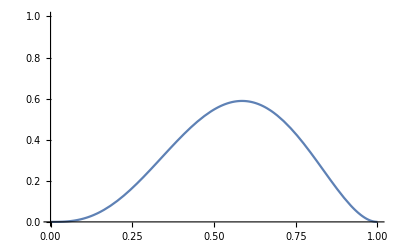

Q[2-√2]//N

0.588745

2-√2//N

0.585786

The maximum occurs when p=0.5858 and Q=0.5887.

ii.	  Find, correct to one decimal place, the value of b for which this maximum occurs.

2 marks

(*Method 1*)
Solve[∫_b^30 1/100(30-t)ⅆt==1-(2-√2),b]//N

{{b→20.8982},{b→39.1018}}

(*Method 2*)
Solve[Probability[T>b,T\[Distributed]d]==1-(2-√2),b]//N

{{b→20.8982}}

b=20.9 mins (reject 39.1 mins as it is outside the domain for 1/100(30-t))

Solve[f’[x]==0,x]

ENDEND

Question 2

-Graphics-